```mathematica
SetDirectory[NotebookDirectory[]];
<< "OpticSimulate.wl"
```

incoming -1.5708 1.5708 -3.14159 -6.80359×10^-17 -6.80359×10^-17

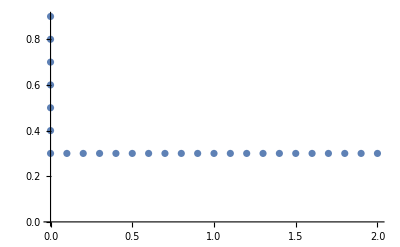

```mathematica
elems = {ConvexLens[0,0,0,1,2]};
elems = GenerateASTs[elems];
ListPlot[SimulBeam[{4,3},elems,{0,1,0,-0.1},75]]
```

```mathematica
OpticRenderStatic[{4,3},{BasicMirror[0,0,0,2]}]
```

-Graphics-

```mathematica
OpticRenderStatic[{4,3},{ConvexLens[0,0,0,3/2,3]}]
```

-Graphics-

1

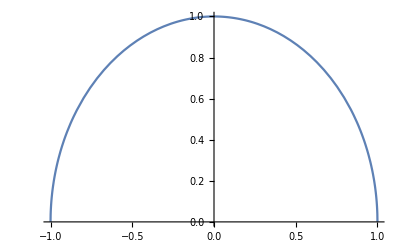

```mathematica
r = 1
exp:=Sqrt[r^2-x^2]-Sqrt[r^2-1^2]
Plot[exp, {x,-1,1}]
(* RegionPlot[0<=y<=exp,{x,-2,2},{y,-2,2}] *)
```

```mathematica
zz
```